Data Stock

108

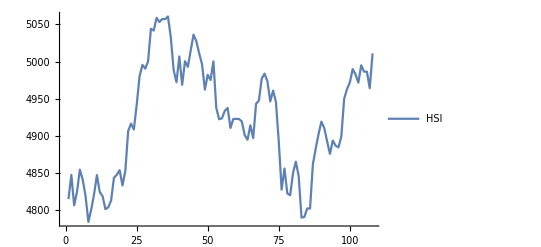

```mathematica
Stock Data

stockData =  FinancialData["^FTSE",{DateObject[{2005,1,1}],DateObject[{2005,6,1}]}];
stockPrices =stockData[[All, 2]];
allRealPrices = stockPrices[[2;;-1]];
allBeforeRealPrices = stockPrices[[1;;-2]];
priceChanges = allRealPrices / allBeforeRealPrices;
Length[stockPrices]
plot = ListLinePlot[{stockPrices},PlotLegends->{"HSI"}]
```

```mathematica
Predictors

sampleSize=40;
windowSize=1;
methods = {"NearestNeighbors", "NeuralNetwork", "RandomForest", "LinearRegression"};
(*methods = {"NeuralNetwork"};*)

iterations = sampleSize;
SetSharedVariable[iterations];
predictedPrices = Monitor[ParallelTable[
iterations++;
patterns = Table[priceChanges[[j;;j+windowSize-1]]->priceChanges[[j+windowSize]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Predict[trainingPatterns, Method ->#, PerformanceGoal->"Quality"]&/@  methods;
(*If [i == sampleSize, Print[PredictorInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]]  * allBeforeRealPrices[[i]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}],ProgressIndicator[iterations, {sampleSize,Length[priceChanges]}]];
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;
AppendTo[methods,"Naive"];
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

Predictors

```mathematica
Predictor results

measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];

mae = Total[Abs[ predictedPrices-realPrices]] / Length[realPrices];
mape = Total[Abs[ predictedPrices/realPrices-1]] / Length[realPrices]*100;

movementAccuracy = Total[(Sign[predictedPrices-beforeRealPrices] * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];

money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] ≥realPrices[[t-1]], 
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
moneyNoFees = money;

money = 1;
hasInvested = True;
For [t = 2, t ≤Length[predictedPrices], t++,
transactionFee = money * 0.14 / 100;

If [hasInvested,
If [predictedPrices[[t]] + transactionFee <realPrices[[t-1]],  
money -= transactionFee;
hasInvested=False;
,
money *= realPrices[[t]] / realPrices[[t-1]];
]
,
If [predictedPrices[[t]] - transactionFee ≥realPrices[[t-1]],  
money = (money-transactionFee)*realPrices[[t]] / realPrices[[t-1]];
hasInvested=True;
]
];

]
AppendTo[measures,{mae, mape, moneyNoFees, money, N[movementAccuracy]}]
]


table = TableForm[measures,TableHeadings->{methods, {"MAE", "MAPE", "Investment profit no fees", "Investment profit", "Movement accuracy"}}]
Export["tidilua.tex", table]

funcs=predictedPricesAllMethodsᵀ;
(*Manipulate[ListLinePlot[fs],{fs,funcs,ControlType->TogglerBar}]*)
Manipulate[ListLinePlot[funcs[[Position[methods, #][[1,1]] & /@ x]], PlotLegends->x], {{x, {"Naive"}, "zebra"},methods, ControlType->TogglerBar}]




(*ListLinePlot[{realPrices, predictedPricesAllMethods[[All,1]], predictedPricesAllMethods[[All,2]], predictedPricesAllMethods[[All,3]], predictedPricesAllMethods[[All,4]]},PlotLegends->{"Real prices", "Predicted Prices"}]*)
```

Predictor results

| MAE | MAPE | Investment profit no fees | Investment profit | Movement accuracy
NearestNeighbors | 21.3601 | 0.433591 | 0.975693 | 0.936846 | 0.426471
NeuralNetwork | 21.4121 | 0.43485 | 0.972162 | 0.943977 | 0.411765
RandomForest | 23.548 | 0.478059 | 1.02291 | 0.976697 | 0.514706
LinearRegression | 20.3644 | 0.413818 | 0.989264 | 0.982358 | 0.455882
Naive | 19.5382 | 0.396997 | 1.00855 | 1.00855 | 0.5

tidilua.tex

```mathematica
funcs[[Position[methods, #][[1,1]] & /@ {"Naive", "NeuralNetwork"}]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {5, {} ⟦ 1, 1 ⟧} cannot be used as a part specification.

{{5015.8,4965.39,5009.89,5000.22,5024.48,5044.28,5039.17,5019.63,5002.37,4957.98,4994.22,4975.69,5004.89,4939.15,4930.47,4929.34,4932.14,4940.41,4908.74,4924.73,4926.14,4923.97,4931.03,4899.8,4898.64,4911.28,4894.77,4930.16,4945.04,4964.86,4982.62,4975.69,4951.01,4952.98,4948.56,4899.31,4832.6,4843.01,4820.68,4823.65,4837.52,4858.37,4837.98,4787.05,4795.62,4796.54,4805.86,4848.66,4869.36,4890.59,4910.53,4915.95,4885.68,4866.89,4887.88,4886.78,4895.15,4894.39,4951.23,4963.69,4982.78,4992.75,4988.05,4969.55,4991.6,4989.9,4997.01,4951.99},{5014.8,4964.33,5008.66,4995.75,5022.03,5044.3,5033.74,5015.37,4999.54,4959.49,4988.49,4978.63,5006.55,4942.97,4925.43,4926.19,4936.63,4940.33,4912.14,4925.18,4923.85,4924.,4920.92,4900.96,4894.85,4906.12,4898.1,4921.1,4944.8,4961.01,4981.77,4975.47,4947.89,4953.75,4947.16,4891.76,4826.18,4843.76,4821.8,4817.36,4837.65,4859.66,4843.13,4785.05,4784.69,4794.89,4798.06,4847.55,4881.47,4902.32,4918.45,4909.47,4889.04,4871.38,4894.32,4883.68,4882.85,4901.77,4955.72,4968.99,4978.16,4997.97,4984.12,4968.68,5003.21,4983.88,4992.06,4951.29},{4994.44,4974.32,5000.77,5009.96,5044.75,5064.22,5052.79,5030.15,4993.12,4965.,5010.28,4995.21,5013.59,4934.5,4914.19,4920.5,4934.53,4921.37,4897.54,4924.71,4928.7,4925.78,4930.36,4913.29,4911.09,4908.68,4902.71,4921.81,4940.42,4953.44,4994.09,4967.04,4946.93,4958.96,4936.8,4884.32,4794.59,4847.8,4840.69,4811.48,4840.15,4854.73,4852.8,4764.65,4792.72,4800.64,4803.92,4866.37,4866.37,4892.32,4903.7,4895.03,4891.73,4892.37,4881.34,4891.89,4901.49,4884.38,4959.2,4991.47,4972.98,4979.07,4983.23,4951.35,5008.74,4971.31,5022.95,4933.54},{5011.13,4972.9,5005.28,4996.56,5019.52,5042.21,5033.83,5016.62,5000.85,4965.23,4986.39,4979.24,5005.61,4941.25,4925.08,4925.49,4935.86,4939.59,4912.52,4924.42,4922.98,4922.72,4919.34,4899.68,4892.22,4911.92,4894.31,4938.9,4944.63,4975.14,4981.78,4971.27,4943.5,4957.51,4943.1,4889.96,4822.99,4852.64,4817.31,4815.8,4845.44,4861.64,4841.19,4783.14,4784.18,4796.38,4796.76,4858.75,4879.98,4900.48,4916.86,4909.65,4891.69,4874.21,4892.32,4885.24,4883.58,4897.94,4952.61,4963.92,4973.66,4992.24,4984.47,4973.1,4997.59,4985.25,4987.33,4962.38},{5006.8,4968.5,5000.5,4992.8,5014.8,5036.3,5027.2,5010.9,4996.1,4962.1,4982.1,4975.,5000.2,4937.6,4922.1,4923.3,4933.5,4937.3,4910.4,4922.5,4922.5,4922.5,4919.,4900.7,4894.4,4914.,4896.7,4942.9,4947.4,4977.,4983.7,4973.3,4946.2,4960.8,4945.4,4891.6,4827.1,4855.6,4822.,4819.6,4849.3,4864.9,4845.5,4789.4,4790.2,4801.7,4801.7,4861.3,4882.5,4902.3,4918.9,4910.3,4892.4,4875.4,4893.3,4886.5,4884.2,4898.5,4949.4,4962.7,4971.8,4989.8,4982.5,4971.5,4994.9,4986.3,4986.3,4964.}}⟦{5,{}⟦1,1⟧}⟧

```mathematica
Classifiers

sampleSize = 30;
windowSize =1;
methods = {"NaiveBayes", "LogisticRegression", "NearestNeighbors", "NeuralNetwork", "SupportVectorMachine","RandomForest"};
methods = {"NeuralNetwork"};
priceChanges = allRealPrices;
predictedPrices = ParallelTable[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->Sign[priceChanges[[j+windowSize]]-priceChanges[[j+windowSize-1]]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Classify[trainingPatterns, Method ->#, PerformanceGoal->"TrainingSpeed"]&/@  methods;
(*If [i == sampleSize, Print[ClassifierInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}]
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

```mathematica
Classifiers results

measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];
movementAccuracy = Total[(predictedPrices * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];
money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] > 0,
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
AppendTo[measures,{N[(money-1),3]*100, N[movementAccuracy,3]*100}]
]


table = TableForm[measures,TableHeadings->{methods, {"Investment profit", "Movement accuracy"}}]

ListPlot
```

| Investment profit | Movement accuracy
NeuralNetwork | -2.03112 | 44.9
Naive | -0.610889 | -7064.94

ListPlot